```mathematica
colorBlindPallete={RGBColor[230/255,159/255,0],RGBColor[86/255,180/255,233/255],RGBColor[0/255,158/255,115/255],RGBColor[240/255,228/255,66/255],RGBColor[0/255,114/255,178/255],RGBColor[213/255,94/255,0/255],RGBColor[204/255,121/255,167/255],RGBColor[0/255,0/255,0/255]};
SetOptions[Plot,BaseStyle->{FontSize->24},ImageSize->Large];
SetOptions[ListPlot,BaseStyle->{FontSize->24,PointSize[Large]},ImageSize->Large];
alpha=20.4*π/180;
beta=68.7*π/180;
deltaAB=alpha-beta;
delta=94.54*π/180 (*Munir's reported 1.66 plus or minus .01*);

alphaOld=3.2*π/180;
betaOld=-6.95*π/180;
rev=1;

Needs["ErrorBarPlots`"]
GenerateListOfFileNames[prefix_,date_,runtimes_]:=Module[{j,fileNames},
fileNames={};
For[j=1,j≤Length[runtimes],j++,
AppendTo[fileNames,StringJoin[prefix,date,"_",ToString[runtimes[[j]]],".dat"]]
];
fileNames
];
(* If given a list of files*)
GetIndexOfFilenameFromTimestamp[files_,timestamp_]:=Module[{i,index},
For[i=1,i≤Length[files],i++,
If[StringContainsQ[ files[[i]],timestamp],index=i]
];
index
];
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
If[Length[rawFile[[k]]]> 2,
association=Append[association,rawFile[[k]][[1]]->StringJoin[ToString[DeleteCases[Take[rawFile[[k]],{2,-1}],Null]]]];
,
association=Append[association,rawFile[[k]][[1]]->rawFile[[k]][[2]]];
];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];
headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
ImportFile[dataFileName_]:={GetFileHeaderInfo[dataFileName],GetFileDataset[dataFileName]}
SetAttributes[GetFileDataset,Listable];
SetAttributes[GetFileHeaderInfo,Listable];
SetAttributes[ImportFile,Listable];

FourierFit[list_,rev_]:=Module[{fit,function,dataPts,stepSize,dataPtsPerRev,angles,data(*,C0,C2,C4,S2,S4*)},

function[θ_]= C0+C2 Cos[2(θ+θo)]+C4 Cos[4(θ+θo)]+S2 Sin[2(θ+θo)]+S4 Sin[4(θ+θo)];
dataPts=Length[list];
dataPtsPerRev=dataPts/rev;
angles=Range[0,(2π*rev)-2π/dataPtsPerRev,2π/dataPtsPerRev];
data=Transpose[{list,angles}];
fit=NonlinearModelFit[data,function[θ],{{C0,1000},C2,C4,S2,S4,θo},θ]
];


DFT[list_,rev_]:=Module[{numItems,i,k,j,reconstructionCos,reconstructionSin,returnCos,errorsCos,returnSin,errorsSin,intensity},
returnCos={};
errorsCos={};
returnSin={};
errorsSin={};
reconstructionCos={};
reconstructionSin={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnCos,0];
AppendTo[returnSin,0];

];

For[i=1,i<=numItems,i++,
intensity=list[[i]];
For [k=0,k<numItems/2,k++,
If[k==0 ||k==(numItems/2-1),
returnCos[[k+1]]=N[returnCos[[k+1]]+1/numItems*intensity*Cos[2*π *k *rev* (i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+1/numItems*intensity*Sin[2*π *k *rev* (i-1)/numItems]];,
returnCos[[k+1]]=N[returnCos[[k+1]]+2/numItems*intensity*Cos[2*π *k* rev *(i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+2/numItems*intensity*Sin[2*π *k* rev *(i-1)/numItems]];
];
];
];
(*

For[j=0,j<numItems/2,j++,
AppendTo[errorsSin,0];
AppendTo[errorsCos,0];
For[i=1,i<=numItems,i++,
intensity=list[[i]];
AppendTo[reconstructionCos,0];
AppendTo[reconstructionSin,0];
reconstructionCos[[i]]=intensity/Cos[2*π*j*rev*(i)/numItems] ;
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]=intensity/Sin[2*π*1.0001*j*rev*(i)/numItems];];
For [k=0,k<numItems/2,k++,
If[k≠j,
reconstructionCos[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(i)/numItems] )/Cos[2*π*j*rev*(i)/numItems];
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(1)/numItems] )/Sin[2*π*1.0001*j*rev*(i)/numItems]];
];
];
errorsSin[[j+1]]+=Power[reconstructionSin[[i]]-returnSin[[j+1]],2];
errorsCos[[j+1]]+=Power[reconstructionCos[[i]]-returnCos[[j+1]],2];
];
errorsSin[[j+1]]=Sqrt[errorsSin[[j+1]]/numItems];
errorsCos[[j+1]]=Sqrt[errorsCos[[j+1]]/numItems];
];
*)
{{returnSin,errorsSin},{returnCos,errorsCos}}
];

StokesParametersFromFourierCoefficients[fc_(*Fourrier Coefficients*),rev_:rev,alpha_:alpha,beta0_:beta,delta_:delta]:=Module[{c0,c2,c4,s2,s4,stokes},
stokes={0,0,0,0,0,0};
c0=fc[[2]][[1]][[1]];
c2=fc[[2]][[1]][[3]];
c4=fc[[2]][[1]][[5]];
s2=fc[[1]][[1]][[3]];
s4=fc[[1]][[1]][[5]];
stokes[[1]]=c0-(1+Cos[delta])/(1-Cos[delta])*(c4*Cos[4 alpha+4 beta0]+s4*Sin[4 alpha+4 beta0]);
stokes[[2]]=2/(1-Cos[delta])*(c4*Cos[2alpha + 4 beta0]+s4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[3]]=2/(1-Cos[delta])*(s4*Cos[2alpha + 4 beta0]-c4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[4]]=Sqrt[c2^2+s2^2]/(Sin[delta]^2 stokes[[1]]);
stokes[[5]]=c2/(Sin[delta]Sin[2 alpha + 4 beta0]stokes[[1]]);
stokes[[6]]=-s2/(Sin[delta]Cos[2 alpha + 4 beta0]stokes[[1]]);
stokes];

StokesParametersFromRawFourierData[intensityArray_,rev_:rev,alpha_:alpha,beta0_:beta,delta_:delta]:=
Module[{fc(*Fourrier Coefficients*),c0,c2,c4,s2,s4,stokes},
fc=DFT[intensityArray,rev];
StokesParametersFromFourierCoefficients[fc,rev,alpha,beta0,delta]
];

StokesParametersFromPolFile[polFile_,alpha_,beta0_,delta_,rev_]:=
Module[{intensityArray,f},
intensityArray=Normal[polFile[[2]][All,"COUNT"]];
StokesParametersFromRawFourierData[intensityArray,rev,alpha,beta0,delta]
];

StokesParametersFromPolFileName[polFileName_,alpha_,beta0_,delta_]:=
Module[{intensityArray,f,rev},
f=ImportFile[polFileName];
intensityArray=Normal[f[[2]][All,"COUNT"]];
rev=f[[1]]["#REV:"];
StokesParametersFromPolFile[f,alpha,beta0,delta,rev_]
];

GetLinearPolarizationFraction[fileName_]:=Module[{data,angle,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
intensity=fc[[2]][[1]];
linearPolarization=Sqrt[(fc[[2]][[3]])^2+(fc[[1]][[3]])^2];
linearPolarizationFraction=linearPolarization/intensity
];
SetAttributes[GetLinearPolarizationFraction,Listable];
GetAngle[fileName_]:=Module[{data,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
.5*ArcTan[fc[[1]][[3]],fc[[2]][[3]]]
];
SetAttributes[GetAngle,Listable];

AverageGetAverageCountRateFromFiles[files_]:=Module[{i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
nDataPts=Length[Normal[files[[1]][[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell;
errorSum[[j]]+=counts[[j]]/nCycles^2*dwell^2;
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

GetAverageCountRateFromFileNames[fileNames_]:=Module[{files},
files=ImportFile[fileNames];
GetAverageCountRateFromFiles[files]
];

(* See Nate Clayburn's explanation on Background Subtraction p. 129 eq. 93*)
(* Returns a list of two items.
	the first item is a list of the intensity reaching the PMT at each step of the polarimeter.
	the second item is the standard deviation of these counts
*)
GetAverageCountRateFromFiles[files_]:=Module[{i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
nDataPts=Length[Normal[files[[1]][[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell;
errorSum[[j]]+=counts[[j]]/nCycles^2*dwell^2;
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];


GetCurrentNormalizedAverageCountRateFromFiles[files_]:=Module[{t,scale,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j,rev},
nDataPts=files[[1]][[1]]["#DATAPPR:"];
rev=files[[1]][[1]]["#REV:"];
(* This hasn't yet been implemented in the data collection files. As soon as it is, you can uncomment it.
scale=files[[1]][[1]]["#SCALE:"];*)
scale=6;
darkCountsRate=10;
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files]*rev;
t=dwell*nCycles;
For[j=1,j≤nDataPts,j++,
sum[[j]]+=(counts[[j]]-darkCountsRate*dwell)/t/Abs[current[[j]]*10^(-scale)/(1*^-9)];
errorSum[[j]]+=(counts[[j]]-darkCountsRate*dwell)/(t^2*(current[[j]]*10^(-scale)/(1*^-9))^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

GetCurrentNormalizedAverageCountRateFromFileNames[fileNames_]:=Module[{filesPass,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
filesPass=ImportFile[fileNames];
GetCurrentNormalizedAverageCountRateFromFiles[filesPass]
];

AverageBackgroundRateCurrentNorm[files_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=GetAverageCountRateFromFiles[darkCountsFiles];
Print[darkCountsRate];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/nCycles/Abs[current[[j]]];
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*current[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

BackgroundRateCurrentNorm[files_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=GetAverageCountRateFromFiles[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/nCycles/Abs[current[[j]]];
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*current[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

AverageSignalRateCurrentNorm[files_,molyCountsRate_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,rev,j},
darkCountsRate=GetAverageCountRateFromFiles[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
rev=files[[i]][[1]]["#REV:"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/rev/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/rev/nCycles/Abs[current[[j]]]-molyCountsRate[[1]][[j]]/rev/nCycles;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*rev^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*rev^2*current[[j]]^2)-molyCountsRate[[2]][[j]]/(nCycles^2*rev^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

SignalRateCurrentNormFromFiles[file_,molyCountFiles_,darkCountsFiles_]:=Module[{molyCountsRate,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=AverageGetAverageCountRateFromFiles[darkCountsFiles];
molyCountsRate=AverageBackgroundRateCurrentNorm[molyCountFiles,darkCountsFiles];
SignalRateCurrentNormFromRates[file,molyCountFiles,darkCountsFiles]
];
SignalRateCurrentNormFromRates::usage ="SignalRateCurrentNormFromRates takes three arguments. First, the file you wish to background subtract, second, the fourier data for the current dependent background, third, the fourier data for the current independent background."
SignalRateCurrentNormFromRates[fileName_,molyCountsRate_,darkCountsRate_]:=Module[{file,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
file=ImportFile[fileName];
nDataPts=Length[Normal[file[[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
counts=Normal[file[[2]][All,"COUNT"]];
current=Normal[file[[2]][All,"CURRENT"]];
dwell=file[[1]]["#DWELL(s):"];
nCycles=file[[1]]["#REV:"];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=(counts[[j]]/(nCycles*dwell)-(darkCountsRate[[1]][[j]])/nCycles)/Abs[current[[j]]]-molyCountsRate[[1]][[j]]/nCycles;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-(darkCountsRate[[2]][[j]])^2/(nCycles^2*current[[j]]^2)-(molyCountsRate[[2]][[j]])^2/(nCycles^2);
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

CalculateOneFileStokes[polFileName_,molyCountRate_,darkCountRate_,alpha_,beta_,delta_]:=Module[{signal,stokes,file,rev},
file=ImportFile[polFileName];
rev=file[[1]]["#REV:"];
signal=SignalRateCurrentNormFromRates[polFileName,molyCountRate,darkCountRate];
StokesParametersFromRawFourierData[signal[[1]],rev,alpha,beta,delta]
];

AverageStokes[stokesVectors_]:=Module[{i,transposedValues,stokes,stokesStdDev},
stokes=stokesVectors[[1]];
stokesStdDev=stokes;
transposedValues=Transpose[stokesVectors];
For[i=1,i≤Length[stokesVectors[[1]]],i++,
stokes[[i]]=Mean[transposedValues[[i]]];
stokesStdDev[[i]]=StandardDeviation[transposedValues[[i]]]/Sqrt[Length[transposedValues]];
];
{stokes,stokesStdDev}
];

CalculateAverageStokesFromFilesAndCountRates[polFileNames_,molyCountRate_,darkCountRate_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{signal,stokes,stokesStdDev,file,rev,j,stokesValues,transposedValues},
stokes={0,0,0,0,0,0};
stokesStdDev={0,0,0,0,0,0};
stokesValues={};
For[j=1,j≤Length[polFileNames],j++,
stokes=CalculateOneFileStokes[polFileNames[[j]],molyCountRate,darkCountRate,alpha,beta,delta];
AppendTo[stokesValues,stokes]
];
Export["stokesValues.tsv",{polFileNames,stokesValues}];
AverageStokes[stokesValues]
]

NormalizeStokes[stokesVector_]:=Module[{intensity,newVector,i},
newVector=stokesVector;
intensity=stokesVector[[1]];
For[i=2,i≤Length[stokesVector],i++,
newVector[[i]]=stokesVector[[i]]/intensity;
];
newVector
];

UnNormalizeStokes[stokesVector_]:=Module[{intensity,newVector,i},
newVector=stokesVector;
intensity=stokesVector[[1]];
For[i=2,i≤Length[stokesVector],i++,
newVector[[i]]=stokesVector[[i]]*intensity;
];
newVector
];

SubtractStokes[addedStokes_,subtractedStokes_]:=Module[
{unNormAdd,unNormSub},
unNormAdd=UnNormalizeStokes[addedStokes];
unNormSub=UnNormalizeStokes[subtractedStokes];
NormalizeStokes[unNormAdd-unNormSub]
];


GetIntensityArrayFromFileName[fileName_]:=Module[{f,intensityArray},
f=ImportFile[fileName];
intensityArray=Normal[f[[2]][All,{"ANGLE","COUNT"}]]
];

PlotRawPolFromFileName[fileName_]:=Module[
{f,intensityArray},
f=ImportFile[fileName];
intensityArray=Normal[f[[2]][All,"COUNT"]];
ListPlot[intensityArray]
];
SetAttributes[PlotRawPolFromFileName,Listable];

PlotListOfPolFileNames[fileNames_,plotRange_:{Automatic,Automatic}]:=Module[{intensityArrays,i},
intensityArrays={};
For[i=1,i≤Length[fileNames],i++,
AppendTo[intensityArrays,Legended[GetIntensityArrayFromFileName[fileNames[[i]]],fileNames[[i]]]];
];
ListPlot[intensityArrays,PlotRange->plotRange]
];

GetStokesFromFileNames[fileNames_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{i,stokes,signal,stokesData},
stokesData={};
signal=ImportFile[fileNames];
For[i=1,i≤Length[fileNames],i++,
stokes=StokesParametersFromPolFile[signal[[i]],alpha,beta,delta,signal[[i]][[1]]["#REV:"]];
AppendTo[stokesData,stokes];
];
stokesData
];
GetAverageFourierCoefficientsFromFileNames[fileNames]:=Module[{fc},
fc=GetFourierCoefficientsFromFileNames[fileNames]];

GetFourierCoefficientsFromFileNames[fileNames_]:=Module[{files,i,coefficientsList,intensityArray,revs},
files=ImportFile[fileNames];
coefficientsList={};
For[i=1,i≤Length[files],i++,
revs=files[[i]][[1]]["#REV:"];
intensityArray=Normal[files[[i]][[2]][All,"COUNT"]];
AppendTo[coefficientsList,DFT[intensityArray,revs]];
];
coefficientsList
];

GetAoutToEnergyModelFromExcitationFunctionTimeStamp[excitationFileNames_,timeStamp_]:=Module[{exFileIndex,exFile,x},
exFileIndex=GetIndexOfFilenameFromTimestamp[excitationFileNames,timeStamp];
exFile=ImportFile[excitationFileNames[[exFileIndex]]];
aoutToElectronEnergyData=Normal[exFile[[2]][All,{"Aout","SecondaryElectronEnergy"}][[All,Values]]];
LinearModelFit[aoutToElectronEnergyData,x,x]
];
```

SignalRateCurrentNormFromRates takes three arguments. First, the file you wish to background subtract, second, the fourier data for the current dependent background, third, the fourier data for the current independent background.

```mathematica
raspberryPi=FileNameJoin[{"Z:","RbData","2017-12-20"}];
dropBoxfolder=FileNameJoin[{"C:","Users","kahrendsen2","Dropbox"}];
dropBoxfolderLaptop=FileNameJoin[{"/","home","karl","Dropbox"}];
dataFolder=FileNameJoin[{"00School","research","DataRuns"}];
folder=FileNameJoin[{dropBoxfolder,dataFolder}];
SetDirectory[folder];
FileNames[]
```

{15-06-09_USBCounterError,15-07-06mockPolarizationData,16-01-14,16-01-21_Data,16-05-25_PolarizationData,16-07-06_PolarizationData,16-08-04_PolarizationData,16-08-07_HeliumTargetPictures,16-08-09_PolarizationData,16-10-17_polarimeter,16-10-27_DataReport,16-11-03_faradayRotation,16-11-07_faradayRotation,16-11-18_faradayRotation,16-12-09_faradayRotation,17-01-31,17-02-17_plusMinus,17-03-06_PlusMinusWavemeter,17-03-10_non-RbFaradayRotation,17-03-15_AimingFor5e12,17-03-15_wavemeterNoRb,17-03-28,17-03-29_pumpLaserFindingCircular,17-03-30_WavemeterReliability,17-04-04_polarization,17-04-06_polarization,17-04-07_wmReliability,17-04-18,17-04-18_polarization,17-04-22,17-04-25_ProbePolarizationDriftOpenChamber,17-04-30_laserReport,17-05-17_DirtyGunRun,17-05-18_ProbeDrift,17-05-19_BetterLaser,17-05-24_SimplifiedPolarization,17-05-25_LaserProfiling,17-06-02,17-06-06_IntensityOfProbeStudy,17-06-11,17-06-13,17-06-16,17-06-17,17-06-25,17-07-01_nRbVsBufferGasAnalysis,17-07-01_PumpLaserAnalysis,17-07-03_lowerNRb_BGPStudy,17-07-03_ProbeDrift,17-07-03_pumpBroadening,17-07-06_lotsOfProbeMeasurements,17-07-06_MagneticField,17-07-06_probePower,17-07-12_polVsPumpPower,17-08-01_rgaInitialScans,17-08-03_redoingSystemDiagnostic,17-08-06_probeDrift,17-08-18_furtherPolarizationStudy,17-08-19_furtherPolarizationStudy2,17-08-22_furtherPolarizationStudyFoundLeak,17-08-29_BvsProbePower_probeDetuneVsMagnetRot,17-09-05_Polarizations_100mTBGP,17-09-20,17-10-03_ElectronGun,17-10-16_ElectronGun,17-10-24_UnpolarizedPolarization,17-10-26_24And30eVRuns,17-10-28_24and30eVRedux,17-11-04_MoreUnpolarizedRuns,17-11-06_UnpolarizedRuns2,17-11-15_BalancedPhotoDetector,17-11-18_SystemDiagnosis,17-12-18_SystemDiagnosis,17-12-20_PolarizingElectrons,18-01-03_PolarizingElectrons,18-01-04_PolarizingElectrons,18-01-10_ChamberWarming,18-01-11_SystemDiagnostics,18-01-12_recreatingPolFigure,18-01-13_recreatingPolFigureIncreasedT,18-01-16_morePolarization,18-01-20_electronPolarization,18-01-25_excitationFunctions,18-01-28_bufferGasPressureVsCounts,18-01-28_exFnCurrentNormalized.png,18-01-28_exFnMolyCounts.png,18-01-28_exFnRawCounts.png,18-01-28_exFnSignalCounts.png,18-01-28_hayesReproduction,18-02-12_polarizedElectrons,18-02-13,18-02-24_DataFrom18-02-13AllElectronEi100,18-02-27,dataDump,pumpQWP,test.png,wavemeterOffsets}

```mathematica
SetDirectory[FileNameJoin[{folder,"18-01-28_hayesReproduction","data"}]];
polFileNames=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]]
excitationFileNames=FileNames[StringExpression["EX",__,"_",__,DigitCharacter,".dat"]]
```

{POL2018-01-28_190002.dat,POL2018-01-28_190526.dat,POL2018-01-28_191053.dat,POL2018-01-28_191620.dat,POL2018-01-28_192146.dat,POL2018-01-28_192713.dat,POL2018-01-28_193240.dat,POL2018-01-28_193806.dat,POL2018-01-28_194333.dat,POL2018-01-28_194900.dat,POL2018-01-28_195428.dat,POL2018-01-28_195955.dat,POL2018-01-28_200522.dat,POL2018-01-28_201048.dat,POL2018-01-28_201615.dat,POL2018-01-28_202142.dat,POL2018-01-28_202708.dat,POL2018-01-28_203235.dat,POL2018-01-28_203802.dat,POL2018-01-28_204328.dat,POL2018-01-28_204855.dat,POL2018-01-28_205421.dat,POL2018-01-28_210222.dat,POL2018-01-28_210748.dat,POL2018-01-28_211315.dat,POL2018-01-28_211842.dat,POL2018-01-28_212408.dat,POL2018-01-28_212935.dat,POL2018-01-28_213502.dat,POL2018-01-28_214028.dat,POL2018-01-28_214555.dat,POL2018-01-28_215121.dat,POL2018-01-28_215648.dat,POL2018-01-28_220215.dat,POL2018-01-28_220741.dat,POL2018-01-28_221308.dat,POL2018-01-28_221834.dat,POL2018-01-28_222401.dat,POL2018-01-28_222928.dat,POL2018-01-28_223454.dat,POL2018-01-28_224021.dat,POL2018-01-28_224548.dat,POL2018-01-28_225114.dat,POL2018-01-28_225641.dat,POL2018-01-28_230442.dat,POL2018-01-28_231008.dat,POL2018-01-28_231535.dat,POL2018-01-28_232101.dat,POL2018-01-28_232628.dat,POL2018-01-28_233154.dat,POL2018-01-28_233721.dat,POL2018-01-28_234248.dat,POL2018-01-28_234814.dat,POL2018-01-28_235345.dat,POL2018-01-28_235912.dat,POL2018-01-29_000438.dat,POL2018-01-29_001005.dat,POL2018-01-29_001532.dat,POL2018-01-29_002058.dat,POL2018-01-29_002625.dat,POL2018-01-29_003151.dat,POL2018-01-29_003718.dat,POL2018-01-29_004245.dat,POL2018-01-29_004811.dat,POL2018-01-29_005338.dat,POL2018-01-29_005907.dat,POL2018-01-29_010433.dat,POL2018-01-29_011000.dat,POL2018-01-29_011527.dat,POL2018-01-29_012053.dat,POL2018-01-29_012620.dat,POL2018-01-29_013147.dat,POL2018-01-29_013713.dat,POL2018-01-29_014240.dat,POL2018-01-29_014806.dat,POL2018-01-29_015333.dat,POL2018-01-29_015900.dat,POL2018-01-29_020426.dat,POL2018-01-29_020953.dat,POL2018-01-29_021519.dat,POL2018-01-29_022046.dat,POL2018-01-29_022613.dat,POL2018-01-29_023139.dat,POL2018-01-29_023706.dat,POL2018-01-29_024233.dat,POL2018-01-29_024759.dat,POL2018-01-29_025326.dat,POL2018-01-29_025852.dat,POL2018-01-29_030419.dat,POL2018-01-29_030946.dat,POL2018-01-29_031512.dat,POL2018-01-29_032039.dat,POL2018-01-29_032606.dat,POL2018-01-29_033132.dat,POL2018-01-29_033659.dat,POL2018-01-29_034226.dat,POL2018-01-29_034752.dat,POL2018-01-29_035319.dat,POL2018-01-29_035845.dat,POL2018-01-29_040412.dat,POL2018-01-29_040939.dat,POL2018-01-29_041505.dat,POL2018-01-29_042032.dat,POL2018-01-29_042558.dat,POL2018-01-29_043125.dat,POL2018-01-29_043652.dat,POL2018-01-29_044218.dat,POL2018-01-29_044745.dat,POL2018-01-29_045312.dat,POL2018-01-29_045838.dat,POL2018-01-29_050405.dat,POL2018-01-29_050931.dat,POL2018-01-29_051458.dat,POL2018-01-29_052025.dat,POL2018-01-29_052551.dat,POL2018-01-29_053118.dat,POL2018-01-29_053645.dat,POL2018-01-29_054211.dat,POL2018-01-29_054738.dat,POL2018-01-29_055305.dat,POL2018-01-29_055831.dat,POL2018-01-29_060358.dat,POL2018-01-29_060925.dat,POL2018-01-29_061451.dat,POL2018-01-29_062018.dat,POL2018-01-29_062545.dat,POL2018-01-29_063111.dat,POL2018-01-29_063638.dat,POL2018-01-29_064204.dat,POL2018-01-29_064731.dat,POL2018-01-29_065258.dat,POL2018-01-29_065824.dat,POL2018-01-29_070351.dat,POL2018-01-29_070918.dat,POL2018-01-29_071444.dat,POL2018-01-29_072011.dat,POL2018-01-29_072537.dat,POL2018-01-29_073104.dat,POL2018-01-29_073631.dat,POL2018-01-29_074157.dat,POL2018-01-29_074724.dat,POL2018-01-29_075250.dat,POL2018-01-29_075817.dat,POL2018-01-29_080344.dat,POL2018-01-29_080910.dat,POL2018-01-29_081437.dat,POL2018-01-29_082004.dat,POL2018-01-29_082530.dat,POL2018-01-29_083057.dat,POL2018-01-29_083623.dat,POL2018-01-29_084150.dat,POL2018-01-29_084717.dat,POL2018-01-29_085243.dat,POL2018-01-29_085810.dat,POL2018-01-29_090337.dat,POL2018-01-29_090903.dat,POL2018-01-29_091430.dat,POL2018-01-29_091956.dat,POL2018-01-29_092523.dat,POL2018-01-29_093050.dat,POL2018-01-29_093616.dat,POL2018-01-29_094143.dat,POL2018-01-29_094710.dat,POL2018-01-29_095236.dat,POL2018-01-29_095803.dat,POL2018-01-29_100329.dat,POL2018-01-29_100856.dat,POL2018-01-29_101423.dat,POL2018-01-29_101949.dat,POL2018-01-29_102516.dat,POL2018-01-29_103043.dat,POL2018-01-29_103609.dat,POL2018-01-29_104136.dat,POL2018-01-29_104703.dat,POL2018-01-29_105229.dat,POL2018-01-29_105756.dat,POL2018-01-29_110322.dat,POL2018-01-29_110849.dat,POL2018-01-29_111416.dat,POL2018-01-29_111942.dat,POL2018-01-29_112509.dat,POL2018-01-29_113038.dat,POL2018-01-29_113605.dat,POL2018-01-29_114131.dat,POL2018-01-29_114658.dat,POL2018-01-29_115224.dat,POL2018-01-29_115751.dat,POL2018-01-29_120318.dat,POL2018-01-29_120844.dat,POL2018-01-29_121411.dat,POL2018-01-29_121938.dat,POL2018-01-29_122505.dat,POL2018-01-29_123031.dat,POL2018-01-29_123558.dat,POL2018-01-29_124125.dat,POL2018-01-29_124651.dat,POL2018-01-29_125218.dat,POL2018-01-29_125745.dat,POL2018-01-29_130311.dat,POL2018-01-29_130838.dat,POL2018-01-29_131404.dat,POL2018-01-29_131931.dat,POL2018-01-29_132458.dat,POL2018-01-29_133024.dat,POL2018-01-29_133551.dat,POL2018-01-29_134118.dat,POL2018-01-29_134644.dat,POL2018-01-29_135211.dat,POL2018-01-29_135738.dat,POL2018-01-29_140304.dat,POL2018-01-29_140831.dat,POL2018-01-29_141358.dat,POL2018-01-29_141924.dat,POL2018-01-29_142451.dat,POL2018-01-29_143018.dat,POL2018-01-29_143544.dat,POL2018-01-29_144111.dat,POL2018-01-29_144638.dat,POL2018-01-29_145204.dat,POL2018-01-29_145731.dat,POL2018-01-29_171422.dat,POL2018-01-29_171949.dat,POL2018-01-29_172516.dat,POL2018-01-29_173042.dat,POL2018-01-29_173609.dat,POL2018-01-29_174136.dat,POL2018-01-29_174702.dat,POL2018-01-29_175229.dat,POL2018-01-29_175756.dat,POL2018-01-29_180322.dat,POL2018-01-29_180849.dat,POL2018-01-29_181416.dat,POL2018-01-29_181942.dat,POL2018-01-29_182509.dat,POL2018-01-29_183036.dat,POL2018-01-29_183602.dat,POL2018-01-29_184131.dat,POL2018-01-29_184658.dat,POL2018-01-29_185227.dat,POL2018-01-29_185753.dat,POL2018-01-29_190320.dat,POL2018-01-29_190847.dat,POL2018-01-29_191649.dat,POL2018-01-29_192215.dat,POL2018-01-29_192741.dat,POL2018-01-29_193308.dat,POL2018-01-29_193835.dat,POL2018-01-29_194401.dat,POL2018-01-29_194928.dat,POL2018-01-29_195454.dat,POL2018-01-29_200021.dat,POL2018-01-29_200548.dat,POL2018-01-29_201114.dat,POL2018-01-29_201641.dat,POL2018-01-29_202208.dat,POL2018-01-29_202734.dat,POL2018-01-29_203301.dat,POL2018-01-29_203828.dat,POL2018-01-29_204354.dat,POL2018-01-29_204921.dat,POL2018-01-29_205447.dat,POL2018-01-29_210014.dat,POL2018-01-29_210541.dat,POL2018-01-29_211107.dat,POL2018-01-29_211910.dat,POL2018-01-29_212435.dat,POL2018-01-29_213002.dat,POL2018-01-29_213529.dat,POL2018-01-29_214055.dat,POL2018-01-29_214622.dat,POL2018-01-29_215149.dat,POL2018-01-29_215715.dat,POL2018-01-29_220242.dat,POL2018-01-29_220809.dat,POL2018-01-29_221335.dat,POL2018-01-29_221902.dat,POL2018-01-29_222428.dat,POL2018-01-29_222955.dat,POL2018-01-29_223522.dat,POL2018-01-29_224048.dat,POL2018-01-29_224615.dat,POL2018-01-29_225142.dat,POL2018-01-29_225710.dat,POL2018-01-29_230237.dat,POL2018-01-29_230803.dat,POL2018-01-29_231330.dat,POL2018-01-29_232132.dat,POL2018-01-29_232658.dat,POL2018-01-29_233225.dat,POL2018-01-29_233752.dat,POL2018-01-29_234318.dat,POL2018-01-29_234845.dat,POL2018-01-29_235411.dat,POL2018-01-29_235938.dat,POL2018-01-30_000505.dat,POL2018-01-30_001031.dat,POL2018-01-30_001558.dat,POL2018-01-30_002125.dat,POL2018-01-30_002651.dat,POL2018-01-30_003218.dat,POL2018-01-30_003745.dat,POL2018-01-30_004311.dat,POL2018-01-30_004838.dat,POL2018-01-30_005404.dat,POL2018-01-30_005931.dat,POL2018-01-30_010458.dat,POL2018-01-30_011024.dat,POL2018-01-30_011551.dat,POL2018-01-30_012726.dat,POL2018-01-30_013251.dat,POL2018-01-30_013818.dat,POL2018-01-30_014345.dat}

{EX2018-01-28_183912.dat,EX2018-01-28_205948.dat,EX2018-01-28_230208.dat,EX2018-01-29_153840.dat,EX2018-01-29_191413.dat,EX2018-01-29_211634.dat,EX2018-01-29_231857.dat,EX2018-01-30_012118.dat,EX2018-01-30_014911.dat}

```mathematica
fit=GetAoutToEnergyModelFromExcitationFunctionTimeStamp[excitationFileNames,"221123"];
fit[516]
fit[324]
fit[36]
```

Part::pkspec1: The expression index$484816 cannot be used as a part specification.

Import::chtype: First argument {EX2018-01-28_183912.dat,EX2018-01-28_205948.dat,EX2018-01-28_230208.dat,EX2018-01-29_153840.dat,EX2018-01-29_191413.dat,EX2018-01-29_211634.dat,EX2018-01-29_231857.dat,EX2018-01-30_012118.dat,EX2018-01-30_014911.dat}⟦index$484816⟧ is not a valid file, directory, or URL specification.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

StringPart::strse: String or list of strings expected at position 1 in StringPart[$Failed,1].

Import::chtype: First argument {EX2018-01-28_183912.dat,EX2018-01-28_205948.dat,EX2018-01-28_230208.dat,EX2018-01-29_153840.dat,EX2018-01-29_191413.dat,EX2018-01-29_211634.dat,EX2018-01-29_231857.dat,EX2018-01-30_012118.dat,EX2018-01-30_014911.dat}⟦index$484816⟧ is not a valid file, directory, or URL specification.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

StringPart::strse: String or list of strings expected at position 1 in StringPart[$Failed,1].

Take::normal: Nonatomic expression expected at position 1 in Take[$Failed,{1,-1},All].

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[{{Missing[KeyAbsent,Aout],Missing[KeyAbsent,SecondaryElectronEnergy]}},x$484815,x$484815][516]

LinearModelFit[{{Missing[KeyAbsent,Aout],Missing[KeyAbsent,SecondaryElectronEnergy]}},x$484815,x$484815][324]

LinearModelFit[{{Missing[KeyAbsent,Aout],Missing[KeyAbsent,SecondaryElectronEnergy]}},x$484815,x$484815][36]

```mathematica
runs=10; (*The number of Electron Polarization Runs*)
aouts=Range[0,630,30]; (* A list of the AOUTs or energies at which we collected data*)
energies=aouts;
aoutToEnergy=GetAoutToEnergyModelFromExcitationFunctionTimeStamp[excitationFileNames,"183912"];
For[i=1,i≤Length[aouts],i++,energies[[i]]=aoutToEnergy[aouts[[i]]]];
startFile=GetIndexOfFilenameFromTimestamp[polFileNames,"190002"];
pumpLights={"noPump"};
fileNames=polFileNames;

category1=pumpLights;
category2=energies;
allFiles=<||>;
subsetFiles=<||>;
files={};
Length[polFileNames]
Length[category1]*Length[category2]*runs

For[j=1,j<=Length[category1],j++,
For[i=1,i<=Length[category2],i++,
firstFile=((startFile-1)+i)+(j-1)*Length[category2];
lastFile=((startFile-1)+i+(j-1)*Length[category2])+(Length[category2]*Length[category1]*(runs-1));
listOfNames=Take[fileNames,{firstFile,lastFile,Length[category1]*Length[category2]}];
AppendTo[subsetFiles,category2[[i]]->listOfNames];
AppendTo[files,<|"cat1"-> category1[[j]],"cat2"->category2[[i]],"fileNames"-> listOfNames|>];
];
AppendTo[allFiles,category1[[j]]->subsetFiles];
];
allFiles;
files
```

312

220

{<|cat1→noPump,cat2→40.,fileNames→{POL2018-01-28_190002.dat,POL2018-01-28_210222.dat,POL2018-01-28_230442.dat,POL2018-01-29_010433.dat,POL2018-01-29_030419.dat,POL2018-01-29_050405.dat,POL2018-01-29_070351.dat,POL2018-01-29_090337.dat,POL2018-01-29_110322.dat,POL2018-01-29_130311.dat}|>,<|cat1→noPump,cat2→39.0698,fileNames→{POL2018-01-28_190526.dat,POL2018-01-28_210748.dat,POL2018-01-28_231008.dat,POL2018-01-29_011000.dat,POL2018-01-29_030946.dat,POL2018-01-29_050931.dat,POL2018-01-29_070918.dat,POL2018-01-29_090903.dat,POL2018-01-29_110849.dat,POL2018-01-29_130838.dat}|>,<|cat1→noPump,cat2→38.1396,fileNames→{POL2018-01-28_191053.dat,POL2018-01-28_211315.dat,POL2018-01-28_231535.dat,POL2018-01-29_011527.dat,POL2018-01-29_031512.dat,POL2018-01-29_051458.dat,POL2018-01-29_071444.dat,POL2018-01-29_091430.dat,POL2018-01-29_111416.dat,POL2018-01-29_131404.dat}|>,<|cat1→noPump,cat2→37.2094,fileNames→{POL2018-01-28_191620.dat,POL2018-01-28_211842.dat,POL2018-01-28_232101.dat,POL2018-01-29_012053.dat,POL2018-01-29_032039.dat,POL2018-01-29_052025.dat,POL2018-01-29_072011.dat,POL2018-01-29_091956.dat,POL2018-01-29_111942.dat,POL2018-01-29_131931.dat}|>,<|cat1→noPump,cat2→36.2792,fileNames→{POL2018-01-28_192146.dat,POL2018-01-28_212408.dat,POL2018-01-28_232628.dat,POL2018-01-29_012620.dat,POL2018-01-29_032606.dat,POL2018-01-29_052551.dat,POL2018-01-29_072537.dat,POL2018-01-29_092523.dat,POL2018-01-29_112509.dat,POL2018-01-29_132458.dat}|>,<|cat1→noPump,cat2→35.349,fileNames→{POL2018-01-28_192713.dat,POL2018-01-28_212935.dat,POL2018-01-28_233154.dat,POL2018-01-29_013147.dat,POL2018-01-29_033132.dat,POL2018-01-29_053118.dat,POL2018-01-29_073104.dat,POL2018-01-29_093050.dat,POL2018-01-29_113038.dat,POL2018-01-29_133024.dat}|>,<|cat1→noPump,cat2→34.4188,fileNames→{POL2018-01-28_193240.dat,POL2018-01-28_213502.dat,POL2018-01-28_233721.dat,POL2018-01-29_013713.dat,POL2018-01-29_033659.dat,POL2018-01-29_053645.dat,POL2018-01-29_073631.dat,POL2018-01-29_093616.dat,POL2018-01-29_113605.dat,POL2018-01-29_133551.dat}|>,<|cat1→noPump,cat2→33.4886,fileNames→{POL2018-01-28_193806.dat,POL2018-01-28_214028.dat,POL2018-01-28_234248.dat,POL2018-01-29_014240.dat,POL2018-01-29_034226.dat,POL2018-01-29_054211.dat,POL2018-01-29_074157.dat,POL2018-01-29_094143.dat,POL2018-01-29_114131.dat,POL2018-01-29_134118.dat}|>,<|cat1→noPump,cat2→32.5584,fileNames→{POL2018-01-28_194333.dat,POL2018-01-28_214555.dat,POL2018-01-28_234814.dat,POL2018-01-29_014806.dat,POL2018-01-29_034752.dat,POL2018-01-29_054738.dat,POL2018-01-29_074724.dat,POL2018-01-29_094710.dat,POL2018-01-29_114658.dat,POL2018-01-29_134644.dat}|>,<|cat1→noPump,cat2→31.6282,fileNames→{POL2018-01-28_194900.dat,POL2018-01-28_215121.dat,POL2018-01-28_235345.dat,POL2018-01-29_015333.dat,POL2018-01-29_035319.dat,POL2018-01-29_055305.dat,POL2018-01-29_075250.dat,POL2018-01-29_095236.dat,POL2018-01-29_115224.dat,POL2018-01-29_135211.dat}|>,<|cat1→noPump,cat2→30.698,fileNames→{POL2018-01-28_195428.dat,POL2018-01-28_215648.dat,POL2018-01-28_235912.dat,POL2018-01-29_015900.dat,POL2018-01-29_035845.dat,POL2018-01-29_055831.dat,POL2018-01-29_075817.dat,POL2018-01-29_095803.dat,POL2018-01-29_115751.dat,POL2018-01-29_135738.dat}|>,<|cat1→noPump,cat2→29.7678,fileNames→{POL2018-01-28_195955.dat,POL2018-01-28_220215.dat,POL2018-01-29_000438.dat,POL2018-01-29_020426.dat,POL2018-01-29_040412.dat,POL2018-01-29_060358.dat,POL2018-01-29_080344.dat,POL2018-01-29_100329.dat,POL2018-01-29_120318.dat,POL2018-01-29_140304.dat}|>,<|cat1→noPump,cat2→28.8376,fileNames→{POL2018-01-28_200522.dat,POL2018-01-28_220741.dat,POL2018-01-29_001005.dat,POL2018-01-29_020953.dat,POL2018-01-29_040939.dat,POL2018-01-29_060925.dat,POL2018-01-29_080910.dat,POL2018-01-29_100856.dat,POL2018-01-29_120844.dat,POL2018-01-29_140831.dat}|>,<|cat1→noPump,cat2→27.9073,fileNames→{POL2018-01-28_201048.dat,POL2018-01-28_221308.dat,POL2018-01-29_001532.dat,POL2018-01-29_021519.dat,POL2018-01-29_041505.dat,POL2018-01-29_061451.dat,POL2018-01-29_081437.dat,POL2018-01-29_101423.dat,POL2018-01-29_121411.dat,POL2018-01-29_141358.dat}|>,<|cat1→noPump,cat2→26.9771,fileNames→{POL2018-01-28_201615.dat,POL2018-01-28_221834.dat,POL2018-01-29_002058.dat,POL2018-01-29_022046.dat,POL2018-01-29_042032.dat,POL2018-01-29_062018.dat,POL2018-01-29_082004.dat,POL2018-01-29_101949.dat,POL2018-01-29_121938.dat,POL2018-01-29_141924.dat}|>,<|cat1→noPump,cat2→26.0469,fileNames→{POL2018-01-28_202142.dat,POL2018-01-28_222401.dat,POL2018-01-29_002625.dat,POL2018-01-29_022613.dat,POL2018-01-29_042558.dat,POL2018-01-29_062545.dat,POL2018-01-29_082530.dat,POL2018-01-29_102516.dat,POL2018-01-29_122505.dat,POL2018-01-29_142451.dat}|>,<|cat1→noPump,cat2→25.1167,fileNames→{POL2018-01-28_202708.dat,POL2018-01-28_222928.dat,POL2018-01-29_003151.dat,POL2018-01-29_023139.dat,POL2018-01-29_043125.dat,POL2018-01-29_063111.dat,POL2018-01-29_083057.dat,POL2018-01-29_103043.dat,POL2018-01-29_123031.dat,POL2018-01-29_143018.dat}|>,<|cat1→noPump,cat2→24.1865,fileNames→{POL2018-01-28_203235.dat,POL2018-01-28_223454.dat,POL2018-01-29_003718.dat,POL2018-01-29_023706.dat,POL2018-01-29_043652.dat,POL2018-01-29_063638.dat,POL2018-01-29_083623.dat,POL2018-01-29_103609.dat,POL2018-01-29_123558.dat,POL2018-01-29_143544.dat}|>,<|cat1→noPump,cat2→23.2563,fileNames→{POL2018-01-28_203802.dat,POL2018-01-28_224021.dat,POL2018-01-29_004245.dat,POL2018-01-29_024233.dat,POL2018-01-29_044218.dat,POL2018-01-29_064204.dat,POL2018-01-29_084150.dat,POL2018-01-29_104136.dat,POL2018-01-29_124125.dat,POL2018-01-29_144111.dat}|>,<|cat1→noPump,cat2→22.3261,fileNames→{POL2018-01-28_204328.dat,POL2018-01-28_224548.dat,POL2018-01-29_004811.dat,POL2018-01-29_024759.dat,POL2018-01-29_044745.dat,POL2018-01-29_064731.dat,POL2018-01-29_084717.dat,POL2018-01-29_104703.dat,POL2018-01-29_124651.dat,POL2018-01-29_144638.dat}|>,<|cat1→noPump,cat2→21.3959,fileNames→{POL2018-01-28_204855.dat,POL2018-01-28_225114.dat,POL2018-01-29_005338.dat,POL2018-01-29_025326.dat,POL2018-01-29_045312.dat,POL2018-01-29_065258.dat,POL2018-01-29_085243.dat,POL2018-01-29_105229.dat,POL2018-01-29_125218.dat,POL2018-01-29_145204.dat}|>,<|cat1→noPump,cat2→20.4657,fileNames→{POL2018-01-28_205421.dat,POL2018-01-28_225641.dat,POL2018-01-29_005907.dat,POL2018-01-29_025852.dat,POL2018-01-29_045838.dat,POL2018-01-29_065824.dat,POL2018-01-29_085810.dat,POL2018-01-29_105756.dat,POL2018-01-29_125745.dat,POL2018-01-29_145731.dat}|>}

```mathematica
allFileNames=Flatten[Normal[Dataset[files][Select[#cat2>26&]][All,"fileNames"]]]
```

{POL2018-01-28_190002.dat,POL2018-01-28_210222.dat,POL2018-01-28_230442.dat,POL2018-01-29_010433.dat,POL2018-01-29_030419.dat,POL2018-01-29_050405.dat,POL2018-01-29_070351.dat,POL2018-01-29_090337.dat,POL2018-01-29_110322.dat,POL2018-01-29_130311.dat,POL2018-01-28_190526.dat,POL2018-01-28_210748.dat,POL2018-01-28_231008.dat,POL2018-01-29_011000.dat,POL2018-01-29_030946.dat,POL2018-01-29_050931.dat,POL2018-01-29_070918.dat,POL2018-01-29_090903.dat,POL2018-01-29_110849.dat,POL2018-01-29_130838.dat,POL2018-01-28_191053.dat,POL2018-01-28_211315.dat,POL2018-01-28_231535.dat,POL2018-01-29_011527.dat,POL2018-01-29_031512.dat,POL2018-01-29_051458.dat,POL2018-01-29_071444.dat,POL2018-01-29_091430.dat,POL2018-01-29_111416.dat,POL2018-01-29_131404.dat,POL2018-01-28_191620.dat,POL2018-01-28_211842.dat,POL2018-01-28_232101.dat,POL2018-01-29_012053.dat,POL2018-01-29_032039.dat,POL2018-01-29_052025.dat,POL2018-01-29_072011.dat,POL2018-01-29_091956.dat,POL2018-01-29_111942.dat,POL2018-01-29_131931.dat,POL2018-01-28_192146.dat,POL2018-01-28_212408.dat,POL2018-01-28_232628.dat,POL2018-01-29_012620.dat,POL2018-01-29_032606.dat,POL2018-01-29_052551.dat,POL2018-01-29_072537.dat,POL2018-01-29_092523.dat,POL2018-01-29_112509.dat,POL2018-01-29_132458.dat,POL2018-01-28_192713.dat,POL2018-01-28_212935.dat,POL2018-01-28_233154.dat,POL2018-01-29_013147.dat,POL2018-01-29_033132.dat,POL2018-01-29_053118.dat,POL2018-01-29_073104.dat,POL2018-01-29_093050.dat,POL2018-01-29_113038.dat,POL2018-01-29_133024.dat,POL2018-01-28_193240.dat,POL2018-01-28_213502.dat,POL2018-01-28_233721.dat,POL2018-01-29_013713.dat,POL2018-01-29_033659.dat,POL2018-01-29_053645.dat,POL2018-01-29_073631.dat,POL2018-01-29_093616.dat,POL2018-01-29_113605.dat,POL2018-01-29_133551.dat,POL2018-01-28_193806.dat,POL2018-01-28_214028.dat,POL2018-01-28_234248.dat,POL2018-01-29_014240.dat,POL2018-01-29_034226.dat,POL2018-01-29_054211.dat,POL2018-01-29_074157.dat,POL2018-01-29_094143.dat,POL2018-01-29_114131.dat,POL2018-01-29_134118.dat,POL2018-01-28_194333.dat,POL2018-01-28_214555.dat,POL2018-01-28_234814.dat,POL2018-01-29_014806.dat,POL2018-01-29_034752.dat,POL2018-01-29_054738.dat,POL2018-01-29_074724.dat,POL2018-01-29_094710.dat,POL2018-01-29_114658.dat,POL2018-01-29_134644.dat,POL2018-01-28_194900.dat,POL2018-01-28_215121.dat,POL2018-01-28_235345.dat,POL2018-01-29_015333.dat,POL2018-01-29_035319.dat,POL2018-01-29_055305.dat,POL2018-01-29_075250.dat,POL2018-01-29_095236.dat,POL2018-01-29_115224.dat,POL2018-01-29_135211.dat,POL2018-01-28_195428.dat,POL2018-01-28_215648.dat,POL2018-01-28_235912.dat,POL2018-01-29_015900.dat,POL2018-01-29_035845.dat,POL2018-01-29_055831.dat,POL2018-01-29_075817.dat,POL2018-01-29_095803.dat,POL2018-01-29_115751.dat,POL2018-01-29_135738.dat,POL2018-01-28_195955.dat,POL2018-01-28_220215.dat,POL2018-01-29_000438.dat,POL2018-01-29_020426.dat,POL2018-01-29_040412.dat,POL2018-01-29_060358.dat,POL2018-01-29_080344.dat,POL2018-01-29_100329.dat,POL2018-01-29_120318.dat,POL2018-01-29_140304.dat,POL2018-01-28_200522.dat,POL2018-01-28_220741.dat,POL2018-01-29_001005.dat,POL2018-01-29_020953.dat,POL2018-01-29_040939.dat,POL2018-01-29_060925.dat,POL2018-01-29_080910.dat,POL2018-01-29_100856.dat,POL2018-01-29_120844.dat,POL2018-01-29_140831.dat,POL2018-01-28_201048.dat,POL2018-01-28_221308.dat,POL2018-01-29_001532.dat,POL2018-01-29_021519.dat,POL2018-01-29_041505.dat,POL2018-01-29_061451.dat,POL2018-01-29_081437.dat,POL2018-01-29_101423.dat,POL2018-01-29_121411.dat,POL2018-01-29_141358.dat,POL2018-01-28_201615.dat,POL2018-01-28_221834.dat,POL2018-01-29_002058.dat,POL2018-01-29_022046.dat,POL2018-01-29_042032.dat,POL2018-01-29_062018.dat,POL2018-01-29_082004.dat,POL2018-01-29_101949.dat,POL2018-01-29_121938.dat,POL2018-01-29_141924.dat,POL2018-01-28_202142.dat,POL2018-01-28_222401.dat,POL2018-01-29_002625.dat,POL2018-01-29_022613.dat,POL2018-01-29_042558.dat,POL2018-01-29_062545.dat,POL2018-01-29_082530.dat,POL2018-01-29_102516.dat,POL2018-01-29_122505.dat,POL2018-01-29_142451.dat}

## Taking the average counts from all the runs and manipulating beta to minimize P_2

```mathematica
cr=DFT[GetAverageCountRateFromFileNames[allFileNames][[1]],1]
alpha=20.4;
Manipulate[ListPlot[StokesParametersFromFourierCoefficients[cr,1,alpha*π/180,beta*π/180,delta],PlotLabel->"Beta ="<>ToString[beta]<>", alpha= "<>ToString[alpha],PlotRange->{Automatic,{-.03,.03}}],{beta,0.001,90,.1}]
```

{{{0.,2.17604,1.87723,0.310123,-8.6617,0.25865,0.0118744,-0.261377,0.194806,-0.177131,0.243353,0.00121767,-0.0340909,-0.0694915,-0.0557318,0.079625,0.194435,0.271252,0.222395,-0.0139218,0.0863139,0.211202,0.167358,0.0088548,0.0818316,-0.1084,0.05713,0.246407,0.255203,-0.00341173},{}},{{536.292,0.549371,1.71201,0.294723,10.3133,-0.0730441,-0.0804263,0.459345,0.190532,0.183128,0.175458,-0.0117248,0.102397,0.176611,0.00821028,0.319958,0.0308353,0.140707,-0.152074,0.0257277,0.337875,-0.186753,0.0726638,0.158983,0.152895,0.115461,-0.195006,0.161444,0.0839269,0.105219},{}}}

## This time, taking all of the no Pump runs and manipulating beta to minimize P3:C2 (5)

```mathematica
cr=DFT[GetAverageCountRateFromFileNames[Join[allFiles[[1]][[2]],allFiles[[1]][[3]],allFiles[[2]][[2]],allFiles[[2]][[3]]]][[1]],1]
Manipulate[ListPlot[StokesParametersFromFourierCoefficients[cr,1,alpha*π/180,beta*π/180,π/2],PlotLabel->"Beta ="<>ToString[beta]<>", alpha= "<>ToString[alpha],PlotRange->{Automatic,{-.1,.1}}],{alpha,0.001,180,.1},{beta,0.001,90,.1}]
```

{{{0.,1.1784,2.62001,0.284943,-17.5553,1.18104,0.503914,0.85219,1.04702,0.738895,0.256199,-0.892243,1.91462,-0.0190515,-1.84368,0.202778,-2.32686,0.192369,-1.19313,0.387646,-1.38444,-1.56172,-1.41061,0.157624,-2.42745,-1.8741,0.565086,-1.77583,0.185493,-0.736445},{}},{{799.559,-1.25906,1.61471,0.651857,18.0906,0.25205,-0.268724,0.605558,1.04297,-0.902889,0.332639,1.91982,0.724006,-1.01814,0.134614,2.09861,-0.330684,1.00172,0.881919,1.65872,-0.771528,-2.33619,0.559578,-1.18869,0.210021,-1.46316,0.250819,1.95389,2.11104,0.200457},{}}}

Part::partd: Part specification cr⟦2⟧ is longer than depth of object.

Part::partd: Part specification cr⟦1⟧ is longer than depth of object.

Part::partd: Part specification cr⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of {{286.136,283.645,279.805,277.572,275.656,274.333,273.382,274.803,276.49,278.558,280.095,282.817,285.097,285.573,285.04,284.448,281.501,278.319,276.207,273.02,«11»,282.289,279.169,276.833,273.191,272.1,272.011,272.013,274.065,276.57,278.939,281.78,283.122,283.969,283.161,282.222,278.644,276.561,273.16,270.971,«10»}} does not exist.

Part::partw: Part 5 of {{286.136,283.645,279.805,277.572,275.656,274.333,273.382,274.803,276.49,278.558,280.095,282.817,285.097,285.573,285.04,284.448,281.501,278.319,276.207,273.02,«11»,282.289,279.169,276.833,273.191,272.1,272.011,272.013,274.065,276.57,278.939,281.78,283.122,283.969,283.161,282.222,278.644,276.561,273.16,270.971,«10»}} does not exist.

Part::partw: Part 3 of {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«10»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 3 of {{286.136,283.645,279.805,277.572,275.656,274.333,273.382,274.803,276.49,278.558,280.095,282.817,285.097,285.573,285.04,284.448,281.501,278.319,276.207,273.02,«11»,282.289,279.169,276.833,273.191,272.1,272.011,272.013,274.065,276.57,278.939,281.78,283.122,283.969,283.161,282.222,278.644,276.561,273.16,270.971,«10»}} does not exist.

Part::partw: Part 5 of {{286.136,283.645,279.805,277.572,275.656,274.333,273.382,274.803,276.49,278.558,280.095,282.817,285.097,285.573,285.04,284.448,281.501,278.319,276.207,273.02,«11»,282.289,279.169,276.833,273.191,272.1,272.011,272.013,274.065,276.57,278.939,281.78,283.122,283.969,283.161,282.222,278.644,276.561,273.16,270.971,«10»}} does not exist.

Part::partw: Part 3 of {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«10»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

## Now all S+ runs, maximize P3:C2

```mathematica
crPlus=DFT[GetAverageCountRateFromFileNames[Join[allFiles[[3]][[2]],allFiles[[3]][[3]]]][[1]],1]
Manipulate[ListPlot[StokesParametersFromFourierCoefficients[crPlus,1,alpha*π/180,beta*π/180,π/2],PlotLabel->"Beta ="<>ToString[beta]<>", alpha= "<>ToString[alpha],PlotRange->{Automatic,{-.1,.1}}],{alpha,0.01,180,.5},{beta,0.01,90,.5}]
```

{{{0.,0.112013,7.86545,0.182234,-17.4846,0.619392,0.172602,0.35258,1.47301,-1.3259,-1.2413,1.23422,-1.06929,0.584217,2.18588,1.15556,1.67486,-1.04522,-0.281918,0.84018,-3.02628,-0.864216,-0.674595,-0.30395,-0.467361,-2.27217,-1.82751,-2.27791,3.32295,-0.708431},{}},{{791.401,-1.22299,4.55841,-1.07074,16.5541,-2.43635,0.854202,-1.64415,2.00489,1.58666,-0.905556,1.67095,2.14285,-0.839731,-1.39715,0.463889,-0.280488,0.292928,-0.527813,0.0968666,-0.697222,-1.56031,-0.105023,-2.84351,-1.65535,-1.3442,-1.6993,-0.586167,3.9673,-0.239907},{}}}

Part::partd: Part specification crPlus⟦2⟧ is longer than depth of object.

Part::partd: Part specification crPlus⟦1⟧ is longer than depth of object.

Part::partd: Part specification crPlus⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

## Now all S- runs, maximize P3:C2

```mathematica
crMinus=DFT[GetAverageCountRateFromFileNames[Join[allFiles[[4]][[2]],allFiles[[4]][[3]]]][[1]],1]
Manipulate[ListPlot[StokesParametersFromFourierCoefficients[crMinus,1,alpha*π/180,beta*π/180,π/2],PlotLabel->"Beta ="<>ToString[beta]<>", alpha= "<>ToString[alpha],PlotRange->{Automatic,{-.1,.1}}],{alpha,0.01,180,.5},{beta,0.01,90,.5}]
```

{{{0.,1.78115,-0.303387,-1.83037,-17.3361,0.163115,1.52605,-0.171453,-0.368338,-1.02368,-1.23842,-0.846395,-3.96541,-2.08349,1.10373,2.17667,-0.707989,0.0903758,0.314222,-0.720683,1.93701,-2.06505,1.00703,1.5837,1.10669,-1.32645,2.50454,0.364977,-0.493443,0.510236},{}},{{794.387,-2.24751,-0.33663,3.08742,17.7552,-0.386699,-2.20388,-1.68475,-2.0385,0.377871,-0.488333,1.05104,3.92549,0.642063,1.66628,0.37,0.513277,1.20567,0.095545,-1.14813,1.38833,0.031484,-0.972415,-2.52234,-2.00382,-0.473301,0.00609991,-2.35011,2.02337,-1.57636},{}}}

Part::partd: Part specification crMinus⟦2⟧ is longer than depth of object.

Part::partd: Part specification crMinus⟦1⟧ is longer than depth of object.

Part::partd: Part specification crMinus⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
colorBlindPallete
```

{RGBColor[Rational[46, 51], Rational[53, 85], 0],RGBColor[Rational[86, 255], Rational[12, 17], Rational[233, 255]],RGBColor[0, Rational[158, 255], Rational[23, 51]],RGBColor[Rational[16, 17], Rational[76, 85], Rational[22, 85]],RGBColor[0, Rational[38, 85], Rational[178, 255]],RGBColor[Rational[71, 85], Rational[94, 255], 0],RGBColor[Rational[4, 5], Rational[121, 255], Rational[167, 255]],RGBColor[0, 0, 0]}

```mathematica
Rasterize[energyPlots[[2]],ImageResolution->200]
```

-Graphics-

## Display all raw data and averages

Pump Light: noPump, Energy: 22.63

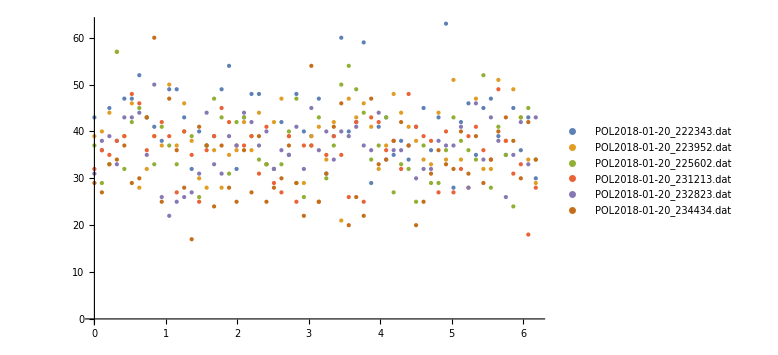

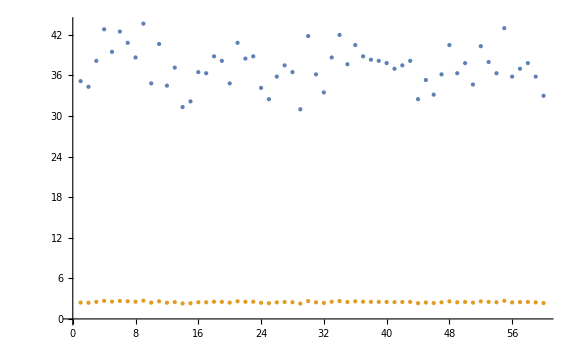

Pump Light: noPump, Energy: 27.49

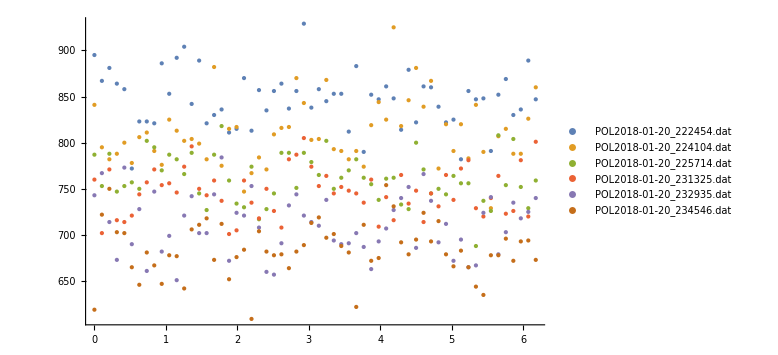

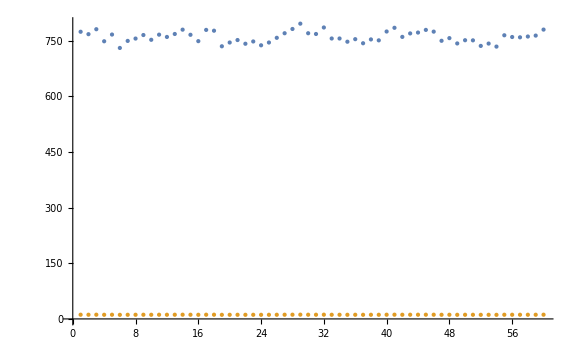

Pump Light: noPump, Energy: 36.55

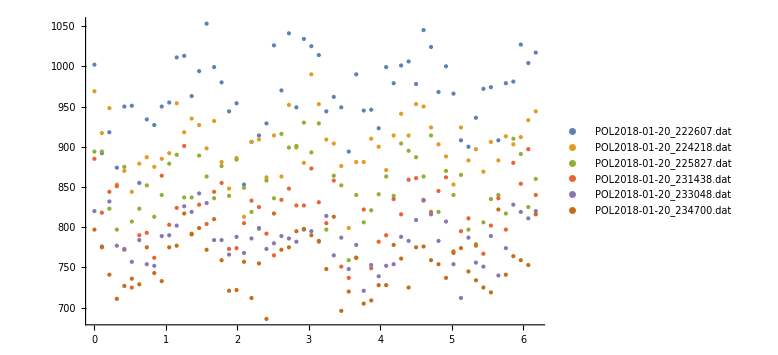

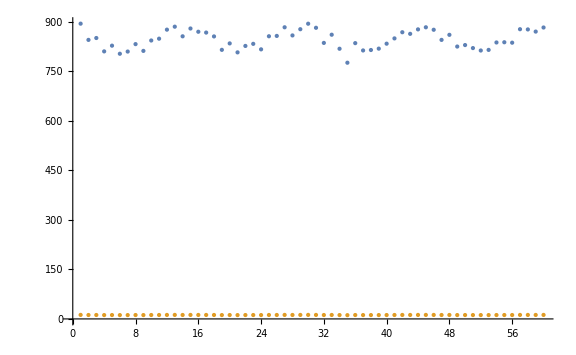

Pump Light: piPump, Energy: 22.63

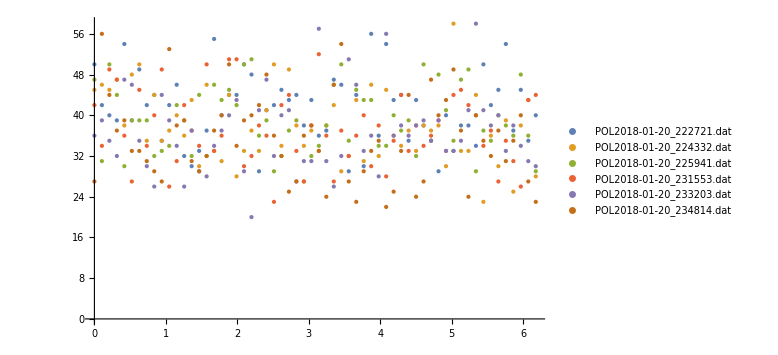

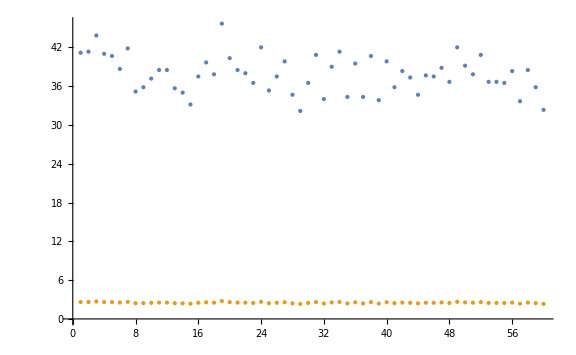

Pump Light: piPump, Energy: 27.49

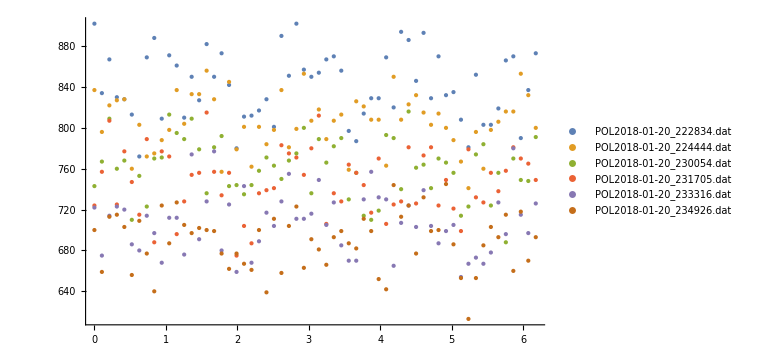

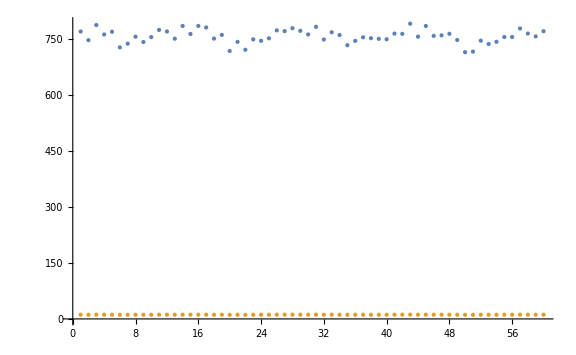

Pump Light: piPump, Energy: 36.55

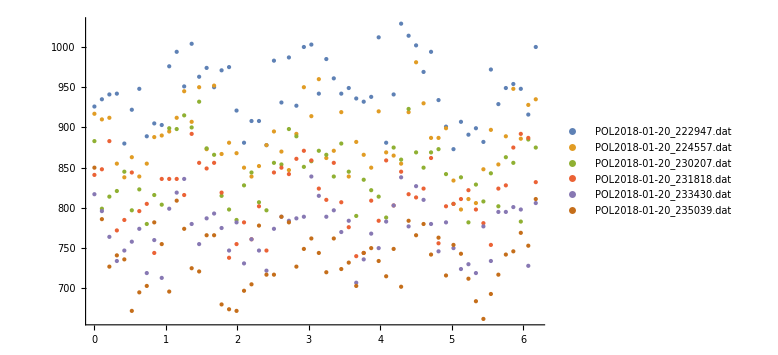

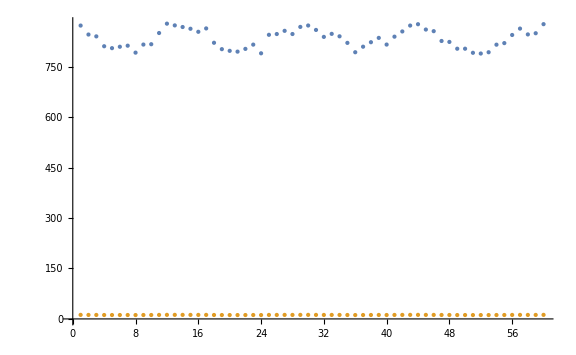

Pump Light: s+Pump, Energy: 22.63

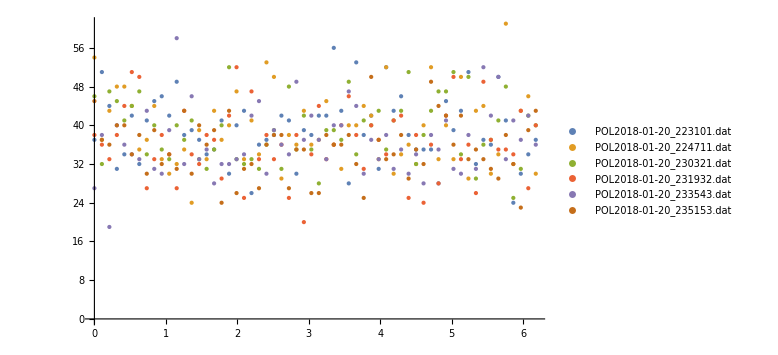

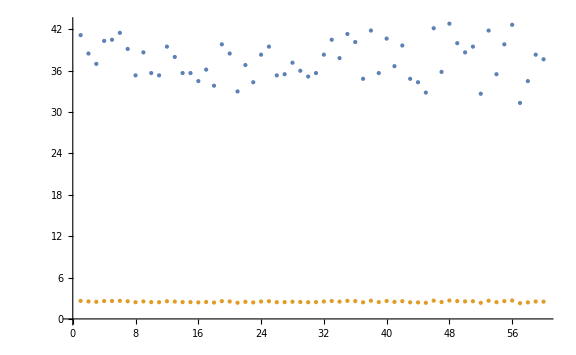

Pump Light: s+Pump, Energy: 27.49

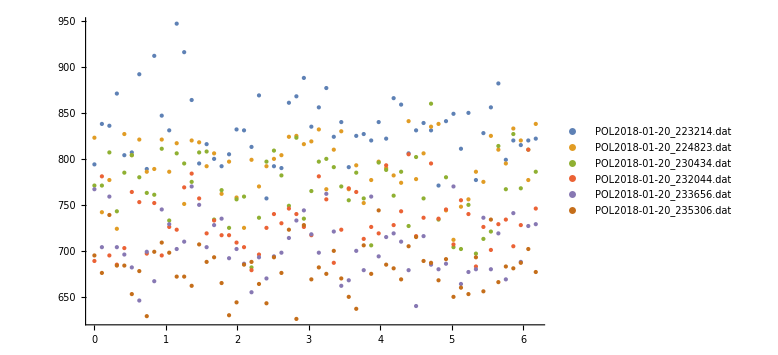

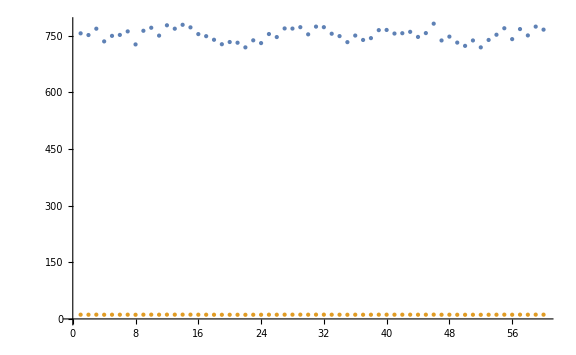

Pump Light: s+Pump, Energy: 36.55

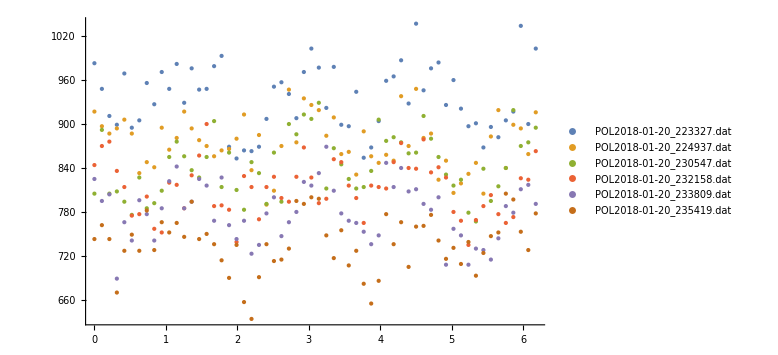

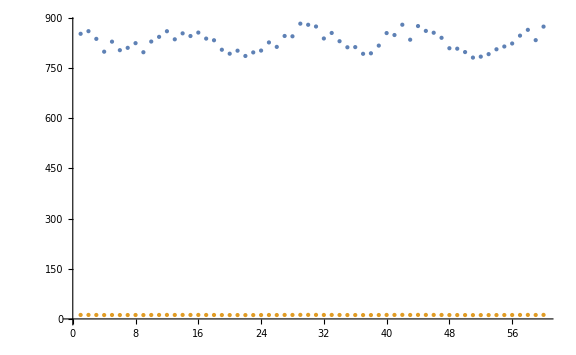

Pump Light: s-Pump, Energy: 22.63

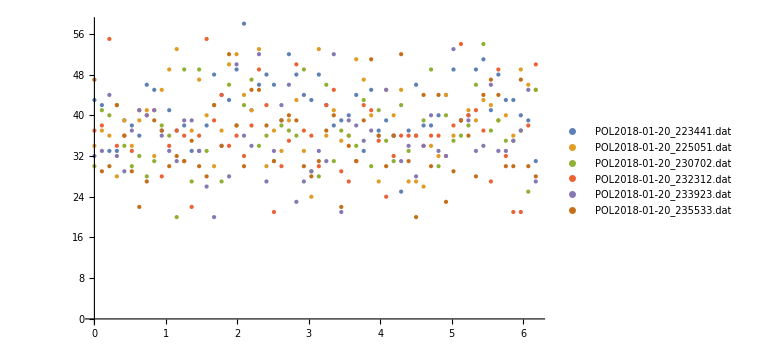

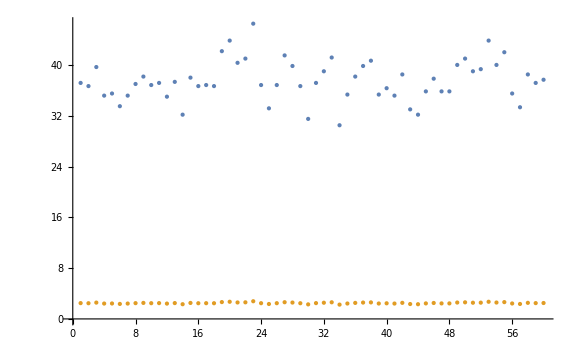

Pump Light: s-Pump, Energy: 27.49

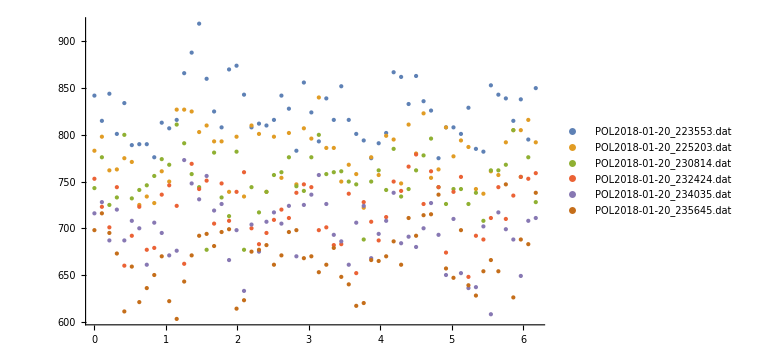

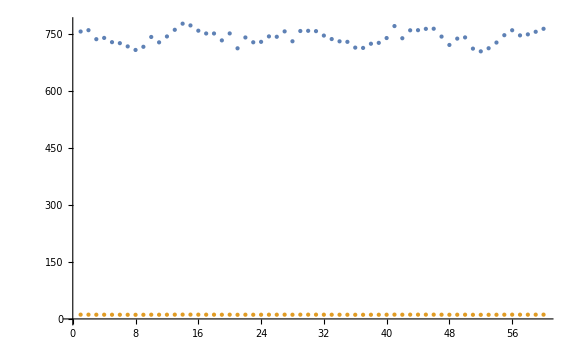

Pump Light: s-Pump, Energy: 36.55

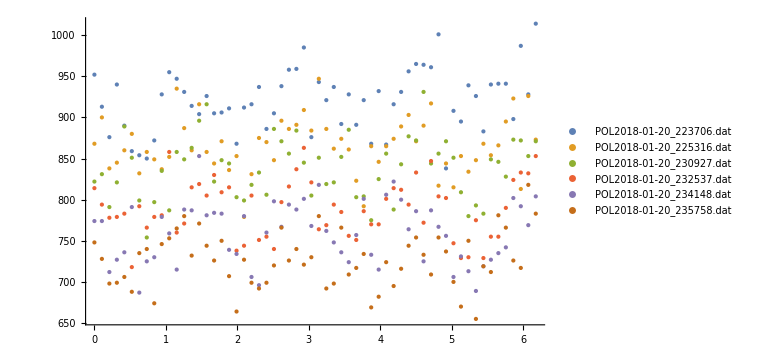

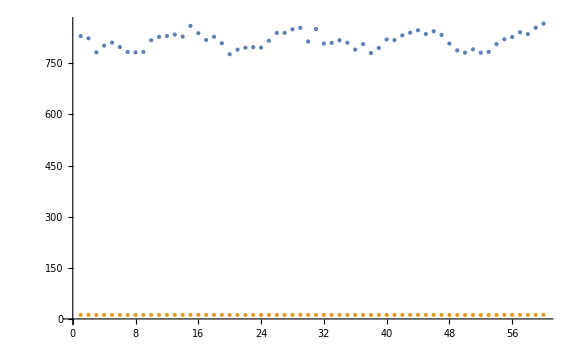

```mathematica
allStokes=<||>;
stokes=<||>;
For[j=1,j<=Length[allFiles],j++,
For[i=1,i<=Length[allFiles[[j]]],i++,
Print["Pump Light: "<>ToString[Keys[allFiles][[j]]]<>", Energy: "<>ToString[Keys[allFiles[[j]]][[i]]]]; 
Print[PlotListOfPolFileNames[allFiles[[j]][[i]]]];
Print[ListPlot[GetAverageCountRateFromFileNames[allFiles[[j]][[i]]]]];
AppendTo[stokes,Keys[allFiles[[j]]][[i]]->GetStokesFromFileNames[allFiles[[j]][[i]]]]
];
AppendTo[allStokes,Keys[allFiles][[j]]->stokes]
];
```

```mathematica
GetIndexOfFilenameFromTimestamp[polFileNames,"223327"]
```

10

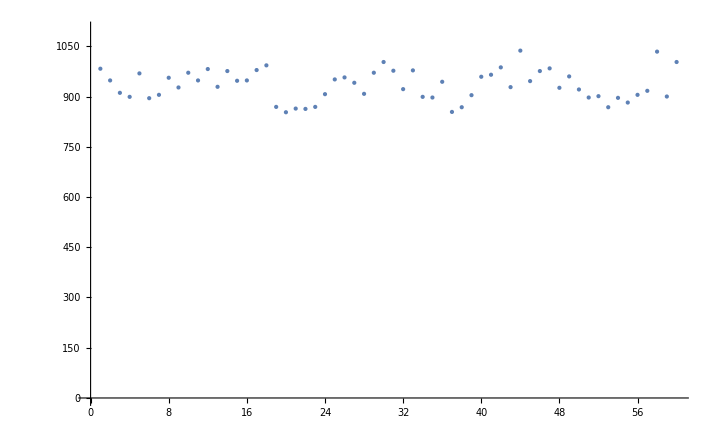

```mathematica
ListPlot[Normal[ImportFile[polFileNames[[10]]][[2]][All,"COUNT"]],PlotRange->{Automatic,{0,1100}}]
```

```mathematica
noPumpLowEng=allFiles["s-Pump"][[1]];
ImportFile[noPumpLowEng[[1]]]
stokes=GetStokesFromFileNames[noPumpLowEng];
ListPlot[Transpose[stokes],PlotLabel-> "Polarization Values Over Time",PlotRange->{-.1,.1},AxesLabel->{"Run Number","Percent Polarization"} ,PlotLegends->{"P_0","P_1","P_2","|P_3|","P_(3  C2)","P_(3  S2)"}];
PlotRawPolFromFileName[noPumpLowEng];
GetFourierCoefficientsFromFileNames[noPumpLowEng];
```

{<|#File→/home/pi/RbData/2018-01-20/POL2018-01-20_223441.dat,#Comments→Run,#IonGauge(Torr):→0.000176,#CVGauge(N2)(Torr):→1.05,#CVGauge(He)(Torr):→0.000984,#CURTEMP_R(degC):→140.,#SETTEMP_R(degC):→140.,#CURTEMP_T(degC):→199.9,#SETTEMP_T(degC):→200.,#AOUT:→516,#LEAKCURR:→0.0002,#AOUTCONV:→0.030938,#REV:→1,#DATAPPR:→60,#STPPERREV:→1200,#DATPTS:→60,#DWELL(s):→1|>,Dataset[<>]}

{<|#File→/home/pi/RbData/2018-01-20/POL2018-01-20_223706.dat,#Comments→Run,#IonGauge(Torr):→0.000176,#CVGauge(N2)(Torr):→1.05,#CVGauge(He)(Torr):→0.000995,#CURTEMP_R(degC):→140.,#SETTEMP_R(degC):→140.,#CURTEMP_T(degC):→199.9,#SETTEMP_T(degC):→199.9,#AOUT:→36,#LEAKCURR:→0.0002,#AOUTCONV:→0.030938,#REV:→1,#DATAPPR:→60,#STPPERREV:→1200,#DATPTS:→60,#DWELL(s):→1|>,Dataset[<>]}

74

145

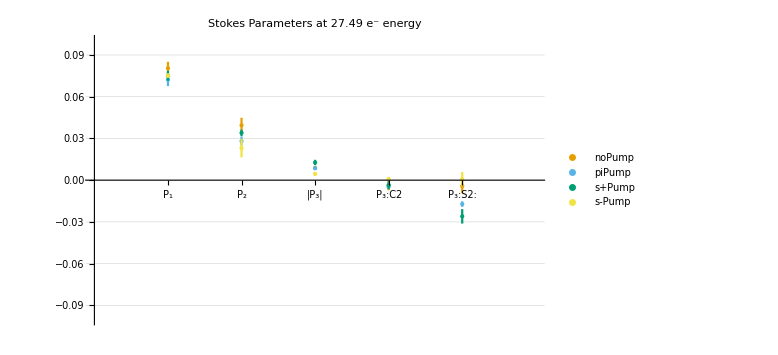
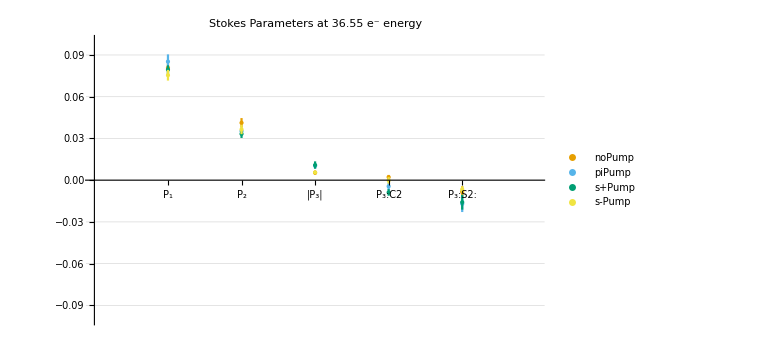
<|27.49→-Graphics-,36.55→-Graphics-|>

```mathematica
runs=6; (*The number of Electron Polarization Runs*)
energies={22.63,27.49,36.55}; (* A list of the AOUTs or energies at which we collected data*)
pumpLights={"noPump","piPump","s+Pump","s-Pump"};
excitationFile=GetIndexOfFilenameFromTimestamp[polFileNames,
startFile=GetIndexOfFilenameFromTimestamp[polFileNames,"013049"]
Length[polFileNames]
fileNames=<||>;
allFiles=<||>;

For[j=0,j<Length[pumpLights],j++,
For[i=startFile,i<Length[energies]+startFile,i++,
listONames=Take[polFileNames,{i+j*Length[energies],i+Length[energies]*runs*Length[pumpLights]-j-(i-startFile)-1,Length[energies]*Length[pumpLights]}];
AppendTo[fileNames,energies[[i-startFile+1]]->listONames];
];
AppendTo[allFiles,pumpLights[[j+1]]->fileNames];
];
allFiles;
energyPlots=<||>;

For[m=2,m≤Length[allFiles[[1]]],m++,
energyIndex=m;
darkCounts={ConstantArray[10,60],ConstantArray[3.3,60]};
stokes=<||>;
For[i=1,i≤Length[Keys[allFiles]],i++,
molyCounts=GetCurrentNormalizedAverageCountRateFromFileNames[allFiles[[i]][[1]]];
AppendTo[stokes,Keys[allFiles][[i]]->CalculateAverageStokesFromFilesAndCountRates[allFiles[[i]][[energyIndex]],molyCounts,darkCounts]];
];

plots={};

For[i=1,i≤Length[stokes],i++,
s=stokes[[i]];
plotData={};
For[k=2,k≤Length[s[[1]]],k++,
AppendTo[plotData,{{k-1,s[[1]][[k]]},ErrorBar[s[[2]][[k]]]}];
];
AppendTo[plots,ErrorListPlot[Legended[plotData,Keys[stokes][[i]]],GridLines->Automatic,ImageSize->{960,600},PlotRange->{{0,6},{-.1,.1}},PlotStyle->colorBlindPallete[[i]],Ticks->{{{1,"P_1"},{2,"P_2"},{3,"|P_3|"},{4,"P_3:C2"},{5,"P_3:S2:"}},Automatic}]];
];
AppendTo[energyPlots,Keys[allFiles[[1]]][[m]]->Show[plots,ImageSize->Large,PlotLabel->"Stokes Parameters at "<>ToString[Keys[allFiles[[1]]][[energyIndex]]]<>" e^- energy"]];
];
energyPlots
```

```mathematica
Rasterize[Show[energyPlots[[1]]],ImageResolution-> 200]
```

-Graphics-